```mathematica
(*REc на отрезке от i-1 до i*)
ClearAll["Global`*"]
Fi[x_]:=ar r^2+br r +cr ;
k =Integrate[polsRR((lambda + 2 mu)*D[Fi[r],r]r +lambda Fi[r]) + polsFF(lambda D[Fi[r],r]r +(lambda + 2 mu) Fi[r]),{r,r1i,rii}]//FullSimplify
CForm[k]
Fi[x_]:=al r^2+bl r +cl;

Integrate[PolsRR((lambda + 2 mu)*D[Fi[r],r]r +lambda Fi[r]) + PolsFF(lambda*D[Fi[r],r]r +(lambda + 2 mu)Fi[r]),{r,ri,ri1}]//FullSimplify;
```

-1/3 (r1i-rii) (3 cr (2 mu polsFF+lambda (polsFF+polsRR))+3 br (lambda+mu) (polsFF+polsRR) (r1i+rii)+ar (3 lambda (polsFF+polsRR)+2 mu (polsFF+2 polsRR)) (r1i^2+r1i rii+rii^2))

-0.3333333333333333*((r1i - rii)*(3*cr*(2*mu*polsFF + lambda*(polsFF + polsRR)) + 3*br*(lambda + mu)*(polsFF + polsRR)*(r1i + rii) + 
       ar*(3*lambda*(polsFF + polsRR) + 2*mu*(polsFF + 2*polsRR))*(Power(r1i,2) + r1i*rii + Power(rii,2))))

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["pols.txt", {Number, Number}];
settings = ReadList["polsSettings.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]];
Pb=settings[[5]];
e=settings[[6]];
nu=settings[[7]];
T = settings[[8]];
M=settings[[9]];
n =3;
p=Pa;
r1=a;r2=b;
exactSigmaRR[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1- r2^(2/n)/r^(2/n))
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b}];
exactSigmaFF[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1+(2-n)/n r2^(2/n)/r^(2/n))
sigmaFFPlot=Plot[exactSigmaFF[r],{r,a,b},PlotStyle->{Red},PlotLegends->{"(σ^c)_ϕϕ"}];
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b},PlotStyle->{Red},PlotLegends->{"(σ^c)_rr"}];

exactSigmaFFUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)+ (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaFFPlotUpr=Plot[exactSigmaFFUpr[r],{r,a,b},PlotStyle->Black,PlotLegends->{"(σ^e)_ϕϕ"}];
exactSigmaRRUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)- (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaRRPlotUpr=Plot[exactSigmaRRUpr[r],{r,a,b},PlotStyle->Black,PlotLegends->{"(σ^e)_rr"}];
numSigmaFF=Import["sigmaFFPols.txt","Table"];
numTableFF={};
numSigmaRR=Import["sigmaRRPols.txt","Table"];
numTableRR={};
For[i =1,i<Length[numSigmaFF],i++,
r=a+h/2;numFF={};numRR={};
For[k=0,k<Length[numSigmaFF[[i]]],k++,
r+=h;
numFF=Append[numFF,{r,numSigmaFF[[i]][[k+1]]}];
numRR=Append[numRR,{r,numSigmaRR[[i]][[k+1]]}];];
numTableRR=Append[numTableRR,numRR];
numTableFF=Append[numTableFF,numFF];
]
```

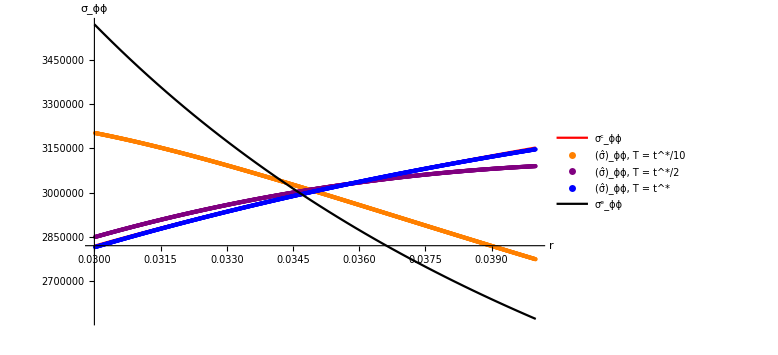

s3.pdf

```mathematica
(*gif=Animate[
Show[ListPlot[numTableFF[[i]]],sigmaFFPlotUpr,sigmaFFPlot],{i,1,M-1,1}]
(*Export["SigmaFF.gif",gif]*)*)
plot200FF= ListPlot[numTableFF[[2017]], PlotStyle->{Blue, PointSize->Small},PlotLegends->{"(σ̂)_ϕϕ, T = t^*"}];
plot1FF= ListPlot[numTableFF[[200]], PlotStyle->{Orange, PointSize->Small},PlotLegends->{"(σ̂)_ϕϕ, T = t^*/10"}];
plotFF= ListPlot[numTableFF[[1000]], PlotStyle->{Purple, PointSize->Small},PlotLegends->{"(σ̂)_ϕϕ, T = t^*/2"}];
s3=Show[sigmaFFPlot,plot1FF,plotFF,plot200FF,sigmaFFPlotUpr,PlotRange->All,ImageSize->Large,PlotTheme->"Classic",AxesLabel->{"r","σ_ϕϕ"},LabelStyle->Directive[Black]]
Export["s3.pdf",s3]
```

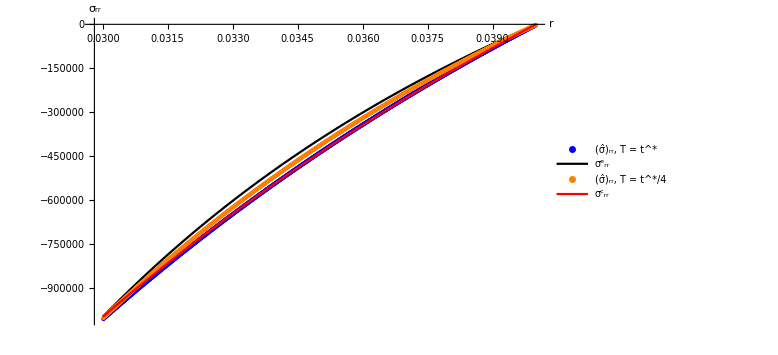

s4.pdf

```mathematica
(*gifRR=Animate[
Show[sigmaRRPlot,ListPlot[numTableRR[[i]]],sigmaRRPlotUpr],{i,1,M-1,1}]
(*Export["SigmaRR.gif",gif]*)*)
plot200RR = ListPlot[numTableRR[[2080]], PlotStyle->{Blue, PointSize->Small},PlotLegends->{"(σ̂)_rr, T = t^*"}];
plot1RR= ListPlot[numTableRR[[500]], PlotStyle->{Orange, PointSize->Small},PlotLegends->{"(σ̂)_rr, T = t^*/4"}];
s4=Show[plot200RR,sigmaRRPlotUpr,plot1RR,sigmaRRPlot,ImageSize->Large,PlotTheme->"Classic",AxesLabel->{"r","σ_rr"},LabelStyle->Directive[Black]]
Export["s4.pdf",s4]
```

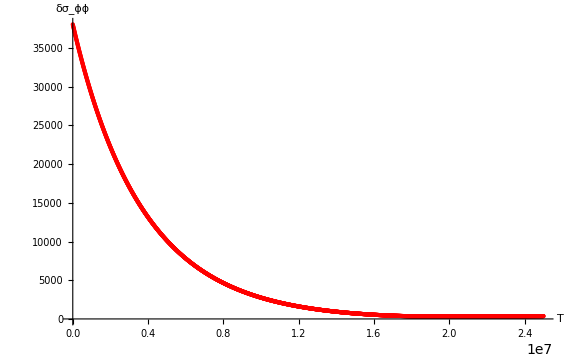

```mathematica
errorLFF=Import["sigmaFFPolsLError.txt","Table"];
l=ListPlot[errorLFF,PlotStyle->Red,ImageSize->Large,PlotTheme->"Classic",AxesLabel->{"T","δσ_ϕϕ"},LabelStyle->Directive[Black]]
```